# Lesson 4: The Limit of a Function

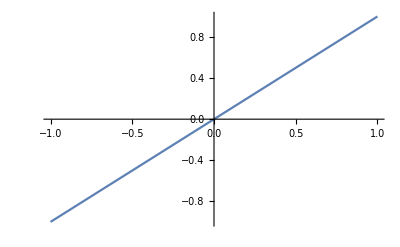

```mathematica
Plot[x,{x,-1,1}]
```

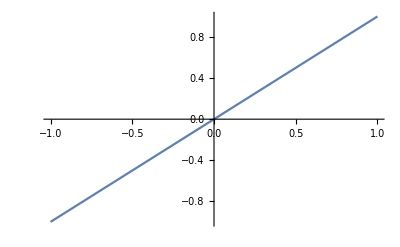

```mathematica
Plot[x^2/x,{x,-1,1}]
```

```mathematica
g[x_]:=x^2/x
```

```mathematica
g[0] //Quiet
```

Indeterminate

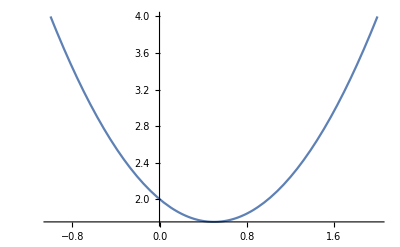

```mathematica
f[x_]:=x^2-x+2
Plot[f[x],{x,-1,2}]
```

```mathematica
limitTablea[function_,xlimit_]:=
Module[{list},list={1,.5,.1,.05,.01,.005,.001};
{TraditionalForm[
Grid[Join[{{"x",function["x"]}},
Transpose[{xlimit-list,function[#]&/@(xlimit-list) //N}]],
Frame->All]],
TraditionalForm[
Grid[Join[{{"x",function["x"]}},
Transpose[{xlimit+list,function[#] &/@(xlimit+list)//N}]],
Frame->All]]}]
limitTablea[f,1] //Quiet
```

{x | x^2-x+2
0 | 2.
0.5 | 1.75
0.9 | 1.91
0.95 | 1.9525
0.99 | 1.9901
0.995 | 1.99503
0.999 | 1.999,x | x^2-x+2
2 | 4.
1.5 | 2.75
1.1 | 2.11
1.05 | 2.0525
1.01 | 2.0101
1.005 | 2.00503
1.001 | 2.001}

```mathematica
Limit[f[x],x->1]
```

2

## Rational Function with a Removable Discontinuity

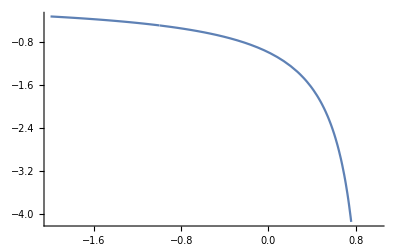

```mathematica
f[x_]:=(x+1)/(x^2-1)

Plot[f[x],{x,-2,1},GridLines->{{-1},{(-1)/2}}]
```

```mathematica
limitTablea[f,-1]
```

{x | (x+1)/(x^2-1)
-2 | -0.333333
-1.5 | -0.4
-1.1 | -0.47619
-1.05 | -0.487805
-1.01 | -0.497512
-1.005 | -0.498753
-1.001 | -0.49975,x | (x+1)/(x^2-1)
0 | -1.
-0.5 | -0.666667
-0.9 | -0.526316
-0.95 | -0.512821
-0.99 | -0.502513
-0.995 | -0.501253
-0.999 | -0.50025}

```mathematica
Limit[f[x],x->-1]
```

-1/2

## Piecewise Function

```mathematica
g[x_]:=Piecewise[{{-.75, x==-1}},
(x+1)/(x^2-1)]
```

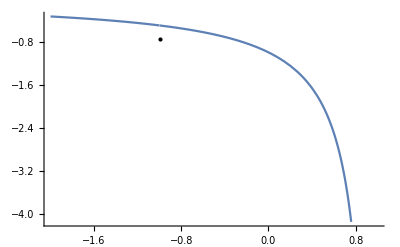

```mathematica
Plot[g[x],{x,-2,1},Sequence[GridLines->{{-1},{-1/2}},
Epilog->{PointSize[Large],Point[{-1,g[-1]}]}]]
```

```mathematica
Limit[g[x],x->-1]
```

-0.5